```mathematica
For[tMin=70;tPrimeMin=tMin;ac=Input["Please input the area of the collector in meters squared."];
ϵL=.7;
mDotCpMin=3400*31*12*3600;
cL=ϵL mDotCpMin;
d=15000*31*12*3600;
ms=100;
cp=4190;
h=-4.002;
k=4.702;
tenv=21;
uas=6;
deltat=31*12*3600;
b=3.85;
c=-0.15;
dd=-1.959;
frPrimeUc=3.5;
hBar=19.16*1000000;
frPrimeταBar=0.72*0.94;
n=31;
kT=0.480;
capitalA=7.10-20.00kT+12.08 kT^2;
capitalB=-8.02+18.16kT-10.68 kT^2;
capitalC=-1.02+4.10kT-1.96 kT^2;
hdbyh=1.317-3.023kT+3.372 kT^2-1.769 kT^3;
frPrimeταn=0.72;
ρg=0.2;
s=39.8;
ll=39.8;
tambPrime=16.8;
z=d/cL;
δ=23.45Sin[360/365(284+135) Degree];
a=0.015((ms*cp/1000)/350)^-0.76;
g=0.2136 ((ms*cp/1000)/350)^-0.704;
f1=((ϵL (mDotCpMin))(tPrimeMin-tMin))/d;

x=ac frPrimeUc (deltat/d);
qu=qMax-a (Exp[b f1] -1)(1-Exp[c x])(Exp[dd z])*d;
hs=ArcCos[-Tan[ll Degree]Tan[δ Degree]];
smallrdn=Pi/24((1-Cos[hs Degree])/(Sin[hs Degree]-(Pi/180)hs Degree Cos[hs Degree]));
smallrn=smallrdn(1.07+.025Sin[hs Degree-60 Degree]);
rB=(Cos[(ll-s) Degree]*Cos[δ Degree]*Cos[hs Degree]+Sin[(ll-s) Degree]*Sin[δ Degree])/(Cos[ll Degree]Cos[δ Degree]*Cos[hs Degree]+Sin[ll Degree]Sin[δ Degree]);
r=(1-hdbyh)rB+hdbyh((1+Cos[s Degree])/2)+ρg((1-Cos[s Degree])/2);
rBn=(Cos[(ll-s) Degree]*Cos[δ Degree]+Sin[(ll-s) Degree]*Sin[δ Degree])/(Cos[ll Degree]Cos[δ Degree]+Sin[ll Degree]Sin[δ Degree]);
rn=(1-smallrdn/smallrn*hdbyh)rBn+(smallrdn/smallrn*hdbyh)((1+Cos[s Degree])/2)+ρg((1-Cos[s Degree])/2);
xcMin=1/(smallrn rn hBar)((frPrimeUc(tPrimeMin-tambPrime))/frPrimeταBar);
ϕMax=Exp[(capitalA+capitalB(rn/r))(xcMin + capitalC xcMin^2)];
htBar=r hBar;
qMax=ac frPrimeταBar htBar n ϕMax;
f2=1/d(qu -uas((tPrimeMin+g(Exp[k f1]-1)Exp[h d/cL])-tenv)deltat),Abs[f1-f2]>0.001,tPrimeMin=tPrimeMin+.001;
f1=((ϵL (mDotCpMin))(tPrimeMin-tMin))/d;

x=ac frPrimeUc (deltat/d);
qu=qMax-a (Exp[b f1] -1)(1-Exp[c x])(Exp[dd z])*d;
hs=ArcCos[-Tan[ll Degree]Tan[δ Degree]];
smallrdn=Pi/24((1-Cos[hs Degree])/(Sin[hs Degree]-(Pi/180)hs Degree Cos[hs Degree]));
smallrn=smallrdn(1.07+.025Sin[hs Degree-60 Degree]);
rB=(Cos[(ll-s) Degree]*Cos[δ Degree]*Cos[hs Degree]+Sin[(ll-s) Degree]*Sin[δ Degree])/(Cos[ll Degree]Cos[δ Degree]*Cos[hs Degree]+Sin[ll Degree]Sin[δ Degree]);
r=(1-hdbyh)rB+hdbyh((1+Cos[s Degree])/2)+ρg((1-Cos[s Degree])/2);
rBn=(Cos[(ll-s) Degree]*Cos[δ Degree]+Sin[(ll-s) Degree]*Sin[δ Degree])/(Cos[ll Degree]Cos[δ Degree]+Sin[ll Degree]Sin[δ Degree]);
rn=(1-smallrdn/smallrn*hdbyh)rBn+(smallrdn/smallrn*hdbyh)((1+Cos[s Degree])/2)+ρg((1-Cos[s Degree])/2);
xcMin=1/(smallrn rn hBar)((frPrimeUc(tPrimeMin-tambPrime))/frPrimeταBar);
ϕMax=Exp[(capitalA+capitalB(rn/r))(xcMin + capitalC xcMin^2)];
htBar=r hBar;
qMax=ac frPrimeταBar htBar n ϕMax;
f2=1/d(qu -uas((tPrimeMin+g(Exp[k f1]-1)Exp[h d/cL])-tenv)deltat),Subscript[c, ac]=f2;]
```

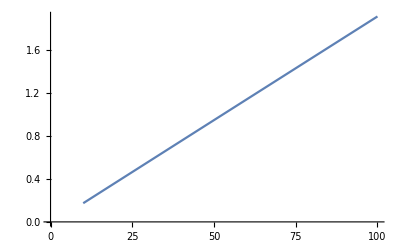

```mathematica
For[ac=10,ac≤100,For[tMin=70;tPrimeMin=tMin;
ϵL=.7;
mDotCpMin=3400*31*12*3600;
cL=ϵL mDotCpMin;
d=15000*31*12*3600;
ms=100;
cp=4190;
h=-4.002;
k=4.702;
tenv=21;
uas=6;
deltat=31*12*3600;
b=3.85;
c=-0.15;
dd=-1.959;
frPrimeUc=3.5;
hBar=19.16*1000000;
frPrimeταBar=0.72*0.94;
n=31;
kT=0.480;
capitalA=7.10-20.00kT+12.08 kT^2;
capitalB=-8.02+18.16kT-10.68 kT^2;
capitalC=-1.02+4.10kT-1.96 kT^2;
hdbyh=1.317-3.023kT+3.372 kT^2-1.769 kT^3;
frPrimeταn=0.72;
ρg=0.2;
s=39.8;
ll=39.8;
tambPrime=16.8;
z=d/cL;
δ=23.45Sin[360/365(284+135) Degree];
a=0.015((ms*cp/1000)/350)^-0.76;
g=0.2136 ((ms*cp/1000)/350)^-0.704;
f1=((ϵL (mDotCpMin))(tPrimeMin-tMin))/d;

x=ac frPrimeUc (deltat/d);
qu=qMax-a (Exp[b f1] -1)(1-Exp[c x])(Exp[dd z])*d;
hs=ArcCos[-Tan[ll Degree]Tan[δ Degree]];
smallrdn=Pi/24((1-Cos[hs Degree])/(Sin[hs Degree]-(Pi/180)hs Degree Cos[hs Degree]));
smallrn=smallrdn(1.07+.025Sin[hs Degree-60 Degree]);
rB=(Cos[(ll-s) Degree]*Cos[δ Degree]*Cos[hs Degree]+Sin[(ll-s) Degree]*Sin[δ Degree])/(Cos[ll Degree]Cos[δ Degree]*Cos[hs Degree]+Sin[ll Degree]Sin[δ Degree]);
r=(1-hdbyh)rB+hdbyh((1+Cos[s Degree])/2)+ρg((1-Cos[s Degree])/2);
rBn=(Cos[(ll-s) Degree]*Cos[δ Degree]+Sin[(ll-s) Degree]*Sin[δ Degree])/(Cos[ll Degree]Cos[δ Degree]+Sin[ll Degree]Sin[δ Degree]);
rn=(1-smallrdn/smallrn*hdbyh)rBn+(smallrdn/smallrn*hdbyh)((1+Cos[s Degree])/2)+ρg((1-Cos[s Degree])/2);
xcMin=1/(smallrn rn hBar)((frPrimeUc(tPrimeMin-tambPrime))/frPrimeταBar);
ϕMax=Exp[(capitalA+capitalB(rn/r))(xcMin + capitalC xcMin^2)];
htBar=r hBar;
qMax=ac frPrimeταBar htBar n ϕMax;
f2=1/d(qu -uas((tPrimeMin+g(Exp[k f1]-1)Exp[h d/cL])-tenv)deltat),Abs[f1-f2]>0.001,tPrimeMin=tPrimeMin+.001;
f1=((ϵL (mDotCpMin))(tPrimeMin-tMin))/d;

x=ac frPrimeUc (deltat/d);
qu=qMax-a (Exp[b f1] -1)(1-Exp[c x])(Exp[dd z])*d;
hs=ArcCos[-Tan[ll Degree]Tan[δ Degree]];
smallrdn=Pi/24((1-Cos[hs Degree])/(Sin[hs Degree]-(Pi/180)hs Degree Cos[hs Degree]));
smallrn=smallrdn(1.07+.025Sin[hs Degree-60 Degree]);
rB=(Cos[(ll-s) Degree]*Cos[δ Degree]*Cos[hs Degree]+Sin[(ll-s) Degree]*Sin[δ Degree])/(Cos[ll Degree]Cos[δ Degree]*Cos[hs Degree]+Sin[ll Degree]Sin[δ Degree]);
r=(1-hdbyh)rB+hdbyh((1+Cos[s Degree])/2)+ρg((1-Cos[s Degree])/2);
rBn=(Cos[(ll-s) Degree]*Cos[δ Degree]+Sin[(ll-s) Degree]*Sin[δ Degree])/(Cos[ll Degree]Cos[δ Degree]+Sin[ll Degree]Sin[δ Degree]);
rn=(1-smallrdn/smallrn*hdbyh)rBn+(smallrdn/smallrn*hdbyh)((1+Cos[s Degree])/2)+ρg((1-Cos[s Degree])/2);
xcMin=1/(smallrn rn hBar)((frPrimeUc(tPrimeMin-tambPrime))/frPrimeταBar);
ϕMax=Exp[(capitalA+capitalB(rn/r))(xcMin + capitalC xcMin^2)];
htBar=r hBar;
qMax=ac frPrimeταBar htBar n ϕMax;
f2=1/d(qu -uas((tPrimeMin+g(Exp[k f1]-1)Exp[h d/cL])-tenv)deltat),Subscript[c, ac]=f2;];ac=ac+10,{}];ListLinePlot[{{10,Subscript[c, 10]},{20,Subscript[c, 20]},{30,Subscript[c, 30]},{40,Subscript[c, 40]},{50,Subscript[c, 50]},{60,Subscript[c, 60]},{70,Subscript[c, 70]},{80,Subscript[c, 80]},{90,Subscript[c, 90]},{100,Subscript[c, 100]}}]
```